```mathematica
Clear[k,L,A,hbar,m]
```

```mathematica
$Assumptions={A>0,L>0,k>0}
```

{A>0,L>0,k>0}

```mathematica
Psi0[x_]:=Exp[-((x-L/4)/k)^2]
```

```mathematica
A0=Integrate[Psi0[x]*Conjugate[Psi0[x]],{x,-Infinity,Infinity}]
```

0.125331-3.83717×10^-16 ⅈ

```mathematica
Psi1[x_]:=Sqrt[1/A0] Exp[-((x-L/4)/k)^2]
```

```mathematica
Integrate[Psi1[x]*Conjugate[Psi00[x]],{x,-Infinity,Infinity}]
```

1

```mathematica
k = 0.1
```

0.1

```mathematica
L = 1
```

1

```mathematica
psi[n_,x_]:=Sqrt[2/L]*Sin[n*Pi*x/L]
```

```mathematica
cn = {}
```

{}

```mathematica
For[i=1,i<=30,i++,cn2=Integrate[psi[i,x]*Psi00[x],{x,0,L}];
AppendTo[cn,cn2];]
```

```mathematica
cnRe = Re[cn]
```

{0.488468,0.641516,0.400985,0.0000306164,-0.270141,-0.291224,-0.149392,0.0000543913,0.0679114,0.0601082,0.025355,0.0000683814,-0.00766665,-0.0055484,-0.00187,0.0000737927,0.000474724,0.000313069,0.000141799,0.0000736011,0.0000635972,0.0000676727,0.0000703606,0.0000704958,0.0000695879,0.0000684673,0.0000673373,0.0000662079,0.0000650717,0.0000639309}

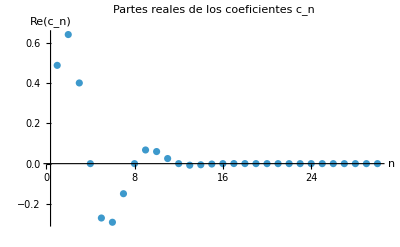

```mathematica
ListPlot[cnRe,AxesLabel->{"n","Re(c_n)"},PlotLabel->"Partes reales de los coeficientes c_n",PlotRange->All]
```

```mathematica
cnIm = Im[cn]
```

{7.47751×10^-16,9.82038×10^-16,6.13831×10^-16,4.68679×10^-20,-4.13534×10^-16,-4.45808×10^-16,-2.28691×10^-16,8.32627×10^-20,1.03959×10^-16,9.20142×10^-17,3.88136×10^-17,1.04679×10^-19,-1.17362×10^-17,-8.49353×10^-18,-2.86262×10^-18,1.12962×10^-19,7.26712×10^-19,4.79249×10^-19,2.17067×10^-19,1.12669×10^-19,9.73552×10^-20,1.03594×10^-19,1.07709×10^-19,1.07916×10^-19,1.06526×10^-19,1.0481×10^-19,1.03081×10^-19,1.01352×10^-19,9.96124×10^-20,9.7866×10^-20}

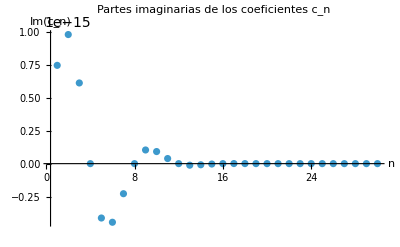

```mathematica
ListPlot[cnIm,AxesLabel->{"n","Im(c_n)"},PlotLabel->"Partes imaginarias de los coeficientes c_n",PlotRange->All]
```

```mathematica
PsiAprox[x_,nTerms_]:=Sum[cn[[n]]*psi[n,x],{n,1,nTerms}]
```

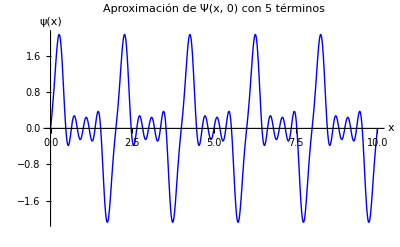

```mathematica
Plot[Re[PsiAprox[x,5]],{x,0,10},PlotStyle->{Thick,Blue},PlotLabel->"Aproximación de Ψ(x, 0) con 5 términos",AxesLabel->{"x","ψ(x)"}]
```

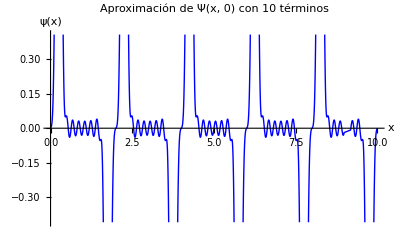

```mathematica
Plot[Re[PsiAprox[x,10]],{x,0,10},PlotStyle->{Thick,Blue},PlotLabel->"Aproximación de Ψ(x, 0) con 10 términos",AxesLabel->{"x","ψ(x)"}]
```

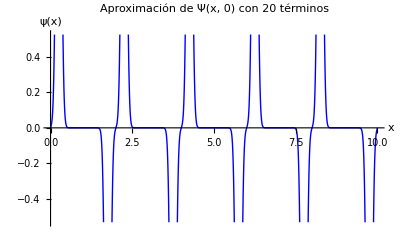

```mathematica
Plot[Re[PsiAprox[x,20]],{x,0,10},PlotStyle->{Thick,Blue},PlotLabel->"Aproximación de Ψ(x, 0) con 20 términos",AxesLabel->{"x","ψ(x)"}]
```

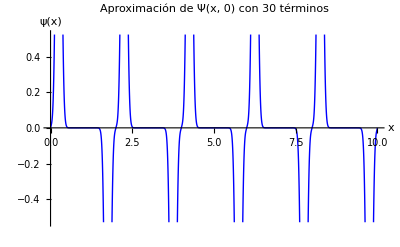

```mathematica
Plot[Re[PsiAprox[x,30]],{x,0,10},PlotStyle->{Thick,Blue},PlotLabel->"Aproximación de Ψ(x, 0) con 30 términos",AxesLabel->{"x","ψ(x)"}]
```

```mathematica
hbar = 1
```

1

```mathematica
m = 1
```

1

```mathematica
En[n_]:=(n^2*Pi^2*hbar^2)/(2*m*L^2)
```

```mathematica
Psi2[x_,t_]:=Sum[cn[[n]]*psi[n,x]*Exp[-I*En[n]*t/hbar],{n,10}]
```

```mathematica
tiempo={0,0.1,0.5,1.0}
```

{0,0.1,0.5,1.}

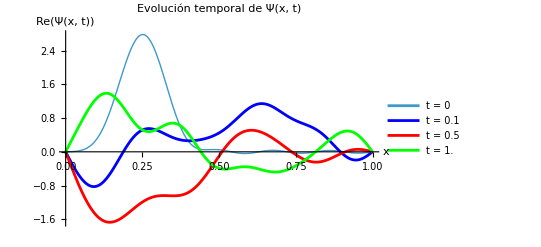

```mathematica
Plot[Evaluate[Table[Re[Psi2[x,t]],{t,tiempo}]],{x,0,L},PlotStyle->{Thick,Blue,Red,Green,Purple},PlotLegends->Table["t = "<>ToString[t],{t,tiempo}],PlotLabel->"Evolución temporal de Ψ(x, t)",AxesLabel->{"x","Re(Ψ(x, t))"}]
```